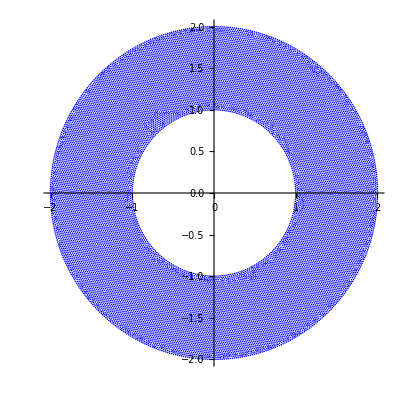

18035

```mathematica
tabve=Import["/Users/michelecastellana/Documents/finite_elements/generate_mesh/2d/ring/solution/vertices.csv"]
tabve=Table[{tabve[[i,1]],tabve[[i,2]]},{i,2,Length[tabve]}]
ListPlot[tabve,PlotStyle->Blue,AspectRatio->1]
Length[tabve]
```

```mathematica
(*write v from ODE to csv file*)
```

```mathematica
tabz=Table[{v[r]/.repv/.sol/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabz,{"f",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution-ode/v_ode.csv",tabz]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution-ode/v_ode.csv

```mathematica
(*write w==0 to csv file*)
```

```mathematica
tabw=Table[{0,tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabw,{"f",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution-ode/w_ode.csv",tabw]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution-ode/w_ode.csv

```mathematica
(*write sigma from ODE to csv file*)
```

```mathematica
tabσ=Table[{σ[r]/.sol/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabσ,{"f",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution-ode/sigma_ode.csv",tabσ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution-ode/sigma_ode.csv

```mathematica
(*write z from ODE to csv file*)
```

```mathematica
tabz=Table[{z[r]/.sol/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabz,{"f",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution-ode/z_ode.csv",tabz]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution-ode/z_ode.csv

```mathematica
(*write omega=z' from ODE to csv file*)
```

```mathematica
tabω=Table[{z'[r]/.sol/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabω,{"f",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution-ode/omega_ode.csv",tabω]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution-ode/omega_ode.csv

```mathematica
(*write mu=H from ODE to csv file*)
```

```mathematica
tabμ=Table[{H[r]/.sol/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabμ,{"f",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution-ode/mu_ode.csv",tabμ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution-ode/mu_ode.csv